## Bose-Hubbard model simulation

References:
	F. Verstraete, V. Murg, J. I. Cirac
	Matrix product states, projected entangled pair states, and variational renormalization group methods for quantum spin systems
	Advances in Physics 57, 143-224 (2008) DOI

	Thomas Barthel
	Precise evaluation of thermal response functions by optimized density matrix renormalization group schemes
	New Journal of Physics 15, 073010 (2013) DOI

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<../mathematica/mps_base.m
```

```mathematica
SparseIdentityMatrix[d_]:=SparseArray[{i_,i_}->1,{d,d}]
```

```mathematica
SiteCreateOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],-1]
SiteAnnihilOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],1]
```

```mathematica
NumberOp[M_]:=DiagonalMatrix[Range[0,M]]
```

```mathematica
Z[H_,β_]:=Norm[MatrixExp[-β/2 H],"Frobenius"]^2
```

```mathematica
(* construct Bose-Hamiltonian with open boundary conditions *)
Subscript[H, bose][t_,U_,μ_,M_,1]:=U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M]
Subscript[H, bose][t_,U_,μ_,M_,L_]:=-t Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],SiteCreateOp[M],SiteAnnihilOp[M],SparseIdentityMatrix[(M+1)^(L-l-1)]]+KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],SiteAnnihilOp[M],SiteCreateOp[M],SparseIdentityMatrix[(M+1)^(L-l-1)]],{l,1,L-1}]+Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M],SparseIdentityMatrix[(M+1)^(L-l)]],{l,1,L}]
```

### Simulation parameters

```mathematica
(* kinetic hopping parameter *)
Subscript[tH, val]=1;
```

```mathematica
(* interaction strength *)
Subscript[U, val]=5;
```

```mathematica
(* chemical potential *)
Subscript[μ, val]=1/7;
```

```mathematica
(* number of lattice sites *)
Subscript[L, val]=5;
```

```mathematica
(* single site occupation number cut-off *)
Subscript[M, val]=2;
```

```mathematica
(* inverse temperature *)
Subscript[β, val]=3/5;
```

```mathematica
Subscript[t, list]=Range[0,5,1/8];
Length[%]
```

41

### Out-of-time-order correlations

```mathematica
OTOC[A_,B_,C_,D_,H_,β_,t_]:=Module[{expβH=MatrixExp[-β H],At=MatrixExp[-ⅈ t H].A.MatrixExp[ⅈ t H],Ct=MatrixExp[-ⅈ t H].C.MatrixExp[ⅈ t H]},1/Z[H,β] Tr[expβH.At.B.Ct.D]]
```

```mathematica
SiteCreateOpFull[n_,M_,L_]:=KroneckerProduct[SparseIdentityMatrix[(M+1)^(n-1)],SiteCreateOp[M],SparseIdentityMatrix[(M+1)^(L-n)]]
```

```mathematica
SiteAnnihilOpFull[n_,M_,L_]:=KroneckerProduct[SparseIdentityMatrix[(M+1)^(n-1)],SiteAnnihilOp[M],SparseIdentityMatrix[(M+1)^(L-n)]]
```

```mathematica
Subscript[fn, import]="../output/bose_hubbard/L"<>ToString[Subscript[L, val]]<>"_otoc/bose_hubbard_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]];
```

```mathematica
(* read simulation results from disk *)
Subscript[otoc, list]=First[#]+ⅈ Last[#]&/@Partition[Import[Subscript[fn, import]<>"_otoc.dat","Real64"],2]
Dimensions[%]
```

{0.455157+0. ⅈ,0.454541-5.56059×10^-6 ⅈ,0.45209-0.000229505 ⅈ,0.446467-0.00146723 ⅈ,0.436317-0.00447577 ⅈ,0.420174-0.00885424 ⅈ,0.395993-0.0132077 ⅈ,0.361811-0.0168429 ⅈ,0.317661-0.0210176 ⅈ,0.266765-0.0281265 ⅈ,0.214428-0.039722 ⅈ,0.165556-0.0555622 ⅈ,0.123249-0.0745381 ⅈ,0.0896335-0.096051 ⅈ,0.0673852-0.119817 ⅈ,0.0592699-0.144169 ⅈ,0.0654518-0.16529 ⅈ,0.0815645-0.179172 ⅈ,0.100466-0.184786 ⅈ,0.116666-0.184784 ⅈ,0.128936-0.182468 ⅈ,0.138242-0.178333 ⅈ,0.143465-0.170216 ⅈ,0.139996-0.156593 ⅈ,0.122988-0.138815 ⅈ,0.0919807-0.11956 ⅈ,0.0521115-0.0994026 ⅈ,0.0108303-0.076014 ⅈ,-0.026287-0.0472115 ⅈ,-0.0573131-0.0139713 ⅈ,-0.083391+0.0198222 ⅈ,-0.107171+0.0497654 ⅈ,-0.131292+0.0725255 ⅈ,-0.157304+0.0853688 ⅈ,-0.184748+0.0852335 ⅈ,-0.210483+0.0698261 ⅈ,-0.229418+0.0406943 ⅈ,-0.237394+0.00487868 ⅈ,-0.234113-0.0278437 ⅈ,-0.222707-0.0500407 ⅈ,-0.206539-0.0588238 ⅈ}

{41}

```mathematica
Subscript[i, site]=2;
Subscript[j, site]=4;
```

```mathematica
(* reference calculation *)
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],HB},HB=N[Subscript[H, bose][tH,U,μ,M,L]];Subscript[otoc, list,ref]=Table[OTOC[SiteCreateOpFull[Subscript[j, site],M,L],SiteCreateOpFull[Subscript[i, site],M,L],SiteAnnihilOpFull[Subscript[j, site],M,L],SiteAnnihilOpFull[Subscript[i, site],M,L],HB,β,t],{t,Subscript[t, list]}]]
```

{0.45511,0.454491-4.44271×10^-6 ⅈ,0.452034-0.000226561 ⅈ,0.446406-0.00145934 ⅈ,0.436259-0.00445984 ⅈ,0.420126-0.00883005 ⅈ,0.395957-0.0131796 ⅈ,0.361788-0.0168166 ⅈ,0.317648-0.0209949 ⅈ,0.266761-0.0281067 ⅈ,0.214431-0.0397053 ⅈ,0.165572-0.055551 ⅈ,0.123279-0.0745352 ⅈ,0.0896724-0.0960569 ⅈ,0.0674216-0.119831 ⅈ,0.0592933-0.144192 ⅈ,0.0654607-0.165321 ⅈ,0.0815647-0.179209 ⅈ,0.100464-0.184822 ⅈ,0.116662-0.184813 ⅈ,0.12893-0.182484 ⅈ,0.138235-0.178334 ⅈ,0.143459-0.170203 ⅈ,0.139992-0.156573 ⅈ,0.122987-0.138796 ⅈ,0.0919784-0.119548 ⅈ,0.0521047-0.0993973 ⅈ,0.0108197-0.0760142 ⅈ,-0.0262979-0.0472167 ⅈ,-0.0573213-0.0139816 ⅈ,-0.0833976+0.0198078 ⅈ,-0.107181+0.0497491 ⅈ,-0.131308+0.0725087 ⅈ,-0.157324+0.0853534 ⅈ,-0.184766+0.0852209 ⅈ,-0.210495+0.0698159 ⅈ,-0.229425+0.0406864 ⅈ,-0.2374+0.00487546 ⅈ,-0.234119-0.027841 ⅈ,-0.222714-0.0500363 ⅈ,-0.206542-0.0588235 ⅈ}

```mathematica
(* compare *)
Abs[Subscript[otoc, list]-Subscript[otoc, list,ref]]
```

{0.0000471583,0.0000496911,0.0000562535,0.0000618532,0.0000605343,0.0000540018,0.0000452609,0.0000349236,0.0000259904,0.0000203842,0.0000170994,0.0000191604,0.0000296925,0.0000392793,0.0000388882,0.0000323102,0.0000324062,0.0000364374,0.0000356164,0.000028918,0.0000172819,7.09692×10^-6,0.0000144426,0.0000207008,0.0000194728,0.0000128364,8.59504×10^-6,0.0000105932,0.0000120922,0.0000132452,0.0000158593,0.000019243,0.0000235141,0.0000249868,0.0000214137,0.0000157732,0.0000108156,6.49552×10^-6,7.01449×10^-6,8.14771×10^-6,3.2014×10^-6}

```mathematica
Subscript[plot, label]="Bose-Hubbard model with\nt_H="<>ToString[Subscript[tH, val]]<>", U="<>ToString[Subscript[U, val]]<>", μ="<>ToString[InputForm[Subscript[μ, val]]]<>", M="<>ToString[Subscript[M, val]]<>", L="<>ToString[Subscript[L, val]]<>", β="<>ToString[N[Subscript[β, val]]]<>"\nsites: i="<>ToString[Subscript[i, site]]<>", j="<>ToString[Subscript[j, site]];
```

```mathematica
Subscript[fn, export]="plots/"<>#<>"/"<>#<>"_"&[FileBaseName[NotebookFileName[]]];
```

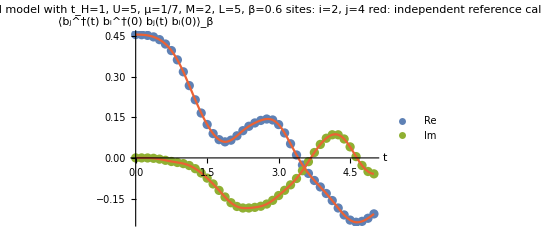

```mathematica
Show[ListPlot[{Transpose[{Subscript[t, list],Re[Subscript[otoc, list]]}],Transpose[{Subscript[t, list],Im[Subscript[otoc, list]]}]},AxesLabel->{"t","⟨b_j^†(t) b_i^†(0) b_j(t) b_i(0)⟩_β"},PlotLabel->Subscript[plot, label]<>"\nred: independent reference calculation",PlotStyle->{ColorData[97][1],ColorData[97][3]},PlotLegends->{"Re","Im"}],Plot[{Interpolation[Transpose[{Subscript[t, list],Re[Subscript[otoc, list,ref]]}]][τ],Interpolation[Transpose[{Subscript[t, list],Im[Subscript[otoc, list,ref]]}]][τ]},{τ,0,5},PlotRange->All,PlotStyle->ColorData[97][4]]]
Export[Subscript[fn, export]<>"otoc1_L"<>ToString[Subscript[L, val]]<>".pdf",%];
```

### Virtual bond dimensions

```mathematica
Subscript[t, plot]={0,1/2,1,2,4,5};
```

{{1,9,30,30,9,1},{1,9,34,39,9,1},{1,9,38,45,9,1},{1,9,43,51,9,1},{1,9,52,58,9,1},{1,9,61,64,9,1},{1,9,69,70,9,1},{1,9,75,73,9,1},{1,9,78,75,9,1},{1,9,80,77,9,1},{1,9,81,79,9,1},{1,9,81,80,9,1},{1,9,81,80,9,1},{1,9,81,80,9,1},{1,9,81,80,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1}}

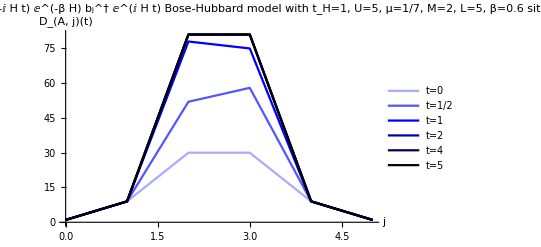

```mathematica
(* virtual bond dimension for 'A' operator *)
Partition[Import[Subscript[fn, import]<>"_DXA.dat","Integer64"],Subscript[L, val]+1]
%⟦#⟧&/@Flatten[Position[Subscript[t, list],#]&/@Subscript[t, plot]];
ListLinePlot[Transpose[{Range[0,Subscript[L, val]],#}]&/@%,AxesLabel->{"j","D_(A, j)(t)"},PlotRange->All,PlotLabel->"virtual bond dimension of ⅇ^(-ⅈ H t) ⅇ^(-β H) b_j^† ⅇ^(ⅈ H t)\n"<>Subscript[plot, label],PlotStyle->{Lighter[Blue,2/3],Lighter[Blue,1/3],Blue,Darker[Blue,1/3],Darker[Blue,2/3],Black},PlotLegends->("t="<>ToString[InputForm[#]]&/@Subscript[t, plot])]
Export[Subscript[fn, export]<>"DA_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>".pdf",%];
```

{{1,1,1,1,1,1},{1,5,11,17,9,1},{1,9,22,32,9,1},{1,9,34,52,9,1},{1,9,61,70,9,1},{1,9,76,77,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1}}

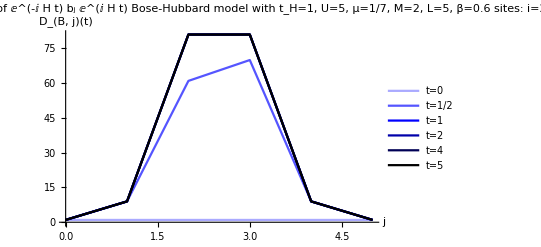

```mathematica
(* virtual bond dimension for 'B' operator *)
Partition[Import[Subscript[fn, import]<>"_DXB.dat","Integer64"],Subscript[L, val]+1]
%⟦#⟧&/@Flatten[Position[Subscript[t, list],#]&/@Subscript[t, plot]];
ListLinePlot[Transpose[{Range[0,Subscript[L, val]],#}]&/@%,AxesLabel->{"j","D_(B, j)(t)"},PlotRange->All,PlotLabel->"virtual bond dimension of ⅇ^(-ⅈ H t) b_j ⅇ^(ⅈ H t)\n"<>Subscript[plot, label],PlotStyle->{Lighter[Blue,2/3],Lighter[Blue,1/3],Blue,Darker[Blue,1/3],Darker[Blue,2/3],Black},PlotLegends->("t="<>ToString[InputForm[#]]&/@Subscript[t, plot])]
Export[Subscript[fn, export]<>"DB_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>".pdf",%];
```

### Effective truncation weight

```mathematica
(* tolerance (truncation weight) for ⅇ^(-β H) *)
Partition[Import[Subscript[fn, import]<>"_tol_eff_beta.dat","Real64"],Subscript[L, val]-1]
```

{{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10}}

```mathematica
(* tolerance (truncation weight) for ⅇ^(-ⅈ H t) ⅇ^(-β H) Subscript[b, j]^† ⅇ^(ⅈ H t) *)
Partition[Import[Subscript[fn, import]<>"_tol_eff_A.dat","Real64"],Subscript[L, val]-1]
Dimensions[%]
```

{{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10}}

{40,4}

```mathematica
(* tolerance (truncation weight) for ⅇ^(-ⅈ H t) Subscript[b, j] ⅇ^(ⅈ H t) *)
Partition[Import[Subscript[fn, import]<>"_tol_eff_B.dat","Real64"],Subscript[L, val]-1]
Dimensions[%]
```

{{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10}}

{40,4}